#### Uses code from 10.08.22 Stabilizing a macroscopic GHZ state

```mathematica
Np=3;
Id=Table[KroneckerDelta[k1,k1p],{k1,0,Np},{k1p,0,Np}];
Sx=Table[KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sy=Table[-I*KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+I*KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sz=Table[KroneckerDelta[k1,k1p]*(2*k1-Np),{k1,0,Np},{k1p,0,Np}];
ghzstate=ArrayReshape[Table[KroneckerDelta[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]];
ghzstate=N[Normalize[ghzstate]];
psi0[k1_,k2_,k3_]=(1/Sqrt[2]^(3*Np))*Sqrt[Binomial[Np,k1]*Binomial[Np,k2]*Binomial[Np,k3]];
psi1[k1_,k2_,k3_]=(1/Sqrt[Np+1])*KroneckerDelta[k1,k2]*(1/Sqrt[2]^(Np))*Sqrt[Binomial[Np,k3]];
Urotzx=KroneckerProduct[MatrixExp[I*Sy*Pi/4],MatrixExp[I*Sy*Pi/4],MatrixExp[I*Sy*Pi/4]];
Idbig=KroneckerProduct[Id,Id,Id];
psivec0=ArrayReshape[Table[psi1[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]];Hamz=2*(KroneckerProduct[Sz.Sz,Id,Id]+KroneckerProduct[Id,Sz.Sz,Id]+KroneckerProduct[Id,Id,Sz.Sz])-2*(KroneckerProduct[Sz,Sz,Id]+KroneckerProduct[Sz,Id,Sz]+KroneckerProduct[Id,Sz,Sz]);
Hamsin=Sin[(KroneckerProduct[Sz,Id,Id]+KroneckerProduct[Id,Sz,Id]+KroneckerProduct[Id,Id,Sz]+(Np-1)*Idbig)*θ];
Hamx=Urotzx.MatrixPower[Hamsin+Idbig,2].ConjugateTranspose[Urotzx];
Hamx1=Urotzx.MatrixPower[-KroneckerProduct[Sz,Id,Id]-KroneckerProduct[Id,Sz,Id]+KroneckerProduct[Id,Id,Sz]+Np*Idbig,2].ConjugateTranspose[Urotzx];
Hamx2=Urotzx.MatrixPower[-KroneckerProduct[Sz,Id,Id]+KroneckerProduct[Id,Sz,Id]-KroneckerProduct[Id,Id,Sz]+Np*Idbig,2].ConjugateTranspose[Urotzx];
Hamx3=Urotzx.MatrixPower[KroneckerProduct[Sz,Id,Id]+KroneckerProduct[Id,Sz,Id]+KroneckerProduct[Id,Id,Sz]+Np*Idbig,2].ConjugateTranspose[Urotzx];
Hamx4=Urotzx.MatrixPower[KroneckerProduct[Sz,Id,Id]-KroneckerProduct[Id,Sz,Id]-KroneckerProduct[Id,Id,Sz]+Np*Idbig,2].ConjugateTranspose[Urotzx];
```

```mathematica
θ=Pi/2;
psi=ArrayReshape[Table[1,{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]];
psip=MatrixExp[-MatrixPower[Hamsin+Idbig,2]*100.0].psi;
For[ns=0,ns≤(Np+1)^3-1,ns=ns+1,
binns=PadLeft[IntegerDigits[ns,Np+1],3];
Print[ns," ",binns," ",Chop[psip[[ns+1]]]," ",Chop[(Urotzx.ghzstate)[[ns+1]]]];
];
```

0 {0,0,0} 0 0.273834

1 {0,0,1} 1. 0

2 {0,0,2} 0 -0.056036

3 {0,0,3} 1. 0

4 {0,1,0} 1. 0

5 {0,1,1} 0 0.209129

6 {0,1,2} 1. 0

7 {0,1,3} 0 -0.056036

8 {0,2,0} 0 -0.056036

9 {0,2,1} 1. 0

10 {0,2,2} 0 0.209129

11 {0,2,3} 1. 0

12 {0,3,0} 1. 0

13 {0,3,1} 0 -0.056036

14 {0,3,2} 1. 0

15 {0,3,3} 0 0.273834

16 {1,0,0} 1. 0

17 {1,0,1} 0 0.209129

18 {1,0,2} 1. 0

19 {1,0,3} 0 -0.056036

20 {1,1,0} 0 0.209129

21 {1,1,1} 1. 0

22 {1,1,2} 0 0.185445

23 {1,1,3} 1. 0

24 {1,2,0} 1. 0

25 {1,2,1} 0 0.185445

26 {1,2,2} 1. 0

27 {1,2,3} 0 0.209129

28 {1,3,0} 0 -0.056036

29 {1,3,1} 1. 0

30 {1,3,2} 0 0.209129

31 {1,3,3} 1. 0

32 {2,0,0} 0 -0.056036

33 {2,0,1} 1. 0

34 {2,0,2} 0 0.209129

35 {2,0,3} 1. 0

36 {2,1,0} 1. 0

37 {2,1,1} 0 0.185445

38 {2,1,2} 1. 0

39 {2,1,3} 0 0.209129

40 {2,2,0} 0 0.209129

41 {2,2,1} 1. 0

42 {2,2,2} 0 0.185445

43 {2,2,3} 1. 0

44 {2,3,0} 1. 0

45 {2,3,1} 0 0.209129

46 {2,3,2} 1. 0

47 {2,3,3} 0 -0.056036

48 {3,0,0} 1. 0

49 {3,0,1} 0 -0.056036

50 {3,0,2} 1. 0

51 {3,0,3} 0 0.273834

52 {3,1,0} 0 -0.056036

53 {3,1,1} 1. 0

54 {3,1,2} 0 0.209129

55 {3,1,3} 1. 0

56 {3,2,0} 1. 0

57 {3,2,1} 0 0.209129

58 {3,2,2} 1. 0

59 {3,2,3} 0 -0.056036

60 {3,3,0} 0 0.273834

61 {3,3,1} 1. 0

62 {3,3,2} 0 -0.056036

63 {3,3,3} 1. 0

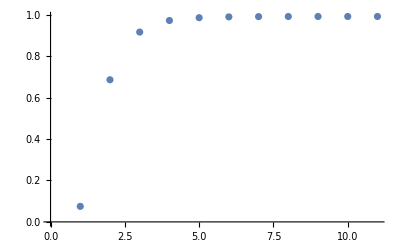

final psi={0.450244,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.545234,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.545234,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.450244}

ghz={0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5}

0.990977

```mathematica
t=10.0;
nrounds=10;
projmatx=MatrixExp[-Hamx2*t];
projmatz=MatrixExp[-Hamz*t];
psi=Normalize[ArrayReshape[Table[psi0[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]]];
fidlist={Abs[Conjugate[ghzstate].psi]^2};
For[n=1,n≤nrounds,n=n+1,
psi=Normalize[projmatz.projmatx.psi];
fidlist=Append[fidlist,Abs[Conjugate[ghzstate].psi]^2];
];
p1=ListPlot[fidlist];
Print[p1];
Print["final psi=",Chop[psi]];
Print["ghz=",ghzstate];
Print[Last[fidlist]];
```

```mathematica
Normalize[Table[1.0*Sqrt[Binomial[Np,k]]^(1/2),{k,0,Np}]]
```

{0.344021,0.486519,0.538422,0.486519,0.344021}

```mathematica
fidlist
```

{0.074985,0.951387,0.997954,0.994139,0.992233,0.99146,0.991165,0.991055,0.991014,0.990999,0.990994}

```mathematica
Total[Total[Abs[projmatx.projmatz-projmatz.projmatx]]]
```

27.4404